# ECH Perpendicular Stratification, B(x)x̂

## Open Additional files:

## Get dispersion routines by evaluating Plasma_Dispersion.np Get plotting and printing routines by evaluating PlotPack.nb Set Parameters by opening a Parameter Window Note: Slab profile models defined in initialization cells at the bottom of this notebook.

### Plot Real and Imaginary parts of n_z from 4nd order cold plasma dispersion relation (Fast and Slow roots)

α = 1.5,  nz = 0.5

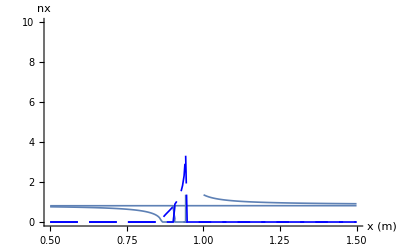

dataSet=Parallel Stratification 28HHz

xProfileMin=0.5

xProfileMax=1.5

nXmin=1.×10^18

nXmax=1.×10^18

BXmin=0.5

BXmax=1.5

freq=28000.

nz=0.5

etaList={0.,1.,0.,0.,0.}

xmin=0.5

xmax=1.5

```mathematica
nPerpFS[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
 nxColdDisFS[freq,ne,b,nz,etaList]];
ntFS=Table[Flatten[{x,nPerpFS[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nF=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[ntFS]⟦2⟧}];
nS=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[ntFS]⟦3⟧}];
g1=PPComplexListPlot[nF,"x (m)","nx"];
g2=PPComplexListPlot[nS,"x (m)","nx"];
Show[{g1,g2},PlotRange->{0.,10.}]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmax}];
```

### Plot Real and Imaginary parts of n_z^2 from 4nd order cold plasma dispersion relation (Fast and Slow roots) N.B. Here n_z is perpendicular to B. But in nzColdDisFS n_z is parallel to B. So think of it as exchanging n_z⟷ n_x.

α = 1.5,  nx = 0.5

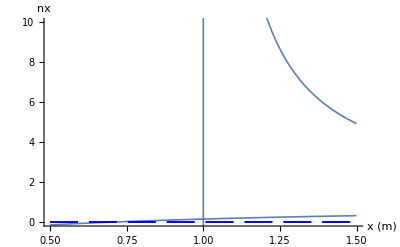

dataSet=Parallel Stratification 28HHz

xProfileMin=0.5

xProfileMax=1.5

nXmin=1.46×10^19

nXmax=1.46×10^19

BXmin=0.5

BXmax=1.5

freq=28000.

nz=0.5

etaList={0.,1.,0.,0.,0.}

xmin=0.5

xmax=1.5

```mathematica
nParallel2FS[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
 nzSqColdDisFS[freq,ne,b,nz,etaList]];
ntFS=Table[Flatten[{x,nParallel2FS[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nF=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[ntFS]⟦2⟧}];
nS=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[ntFS]⟦3⟧}];
g1=PPComplexListPlot[nF,"x (m)","nx"];
g2=PPComplexListPlot[nS,"x (m)","nx"];
Show[{g1,g2},PlotRange->{0.,10.}]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmax}];
```

### Plot Real and Imaginary parts of n_z from 4nd order cold plasma dispersion relation (Plus and Minus roots) N.B. Here n_z is perpendicular to B. But in nzColdDisPM n_z is parallel to B. So think of it as exchanging n_z⟷ n_x.

α = 1.5,  nx = 0.

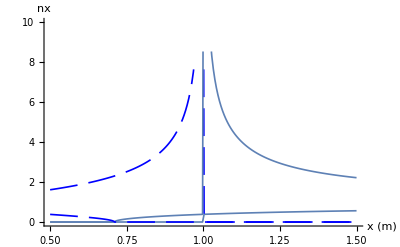

dataSet=Parallel Stratification 28HHz

xProfileMin=0.5

xProfileMax=1.5

nXmin=1.46×10^19

nXmax=1.46×10^19

BXmin=0.5

BXmax=1.5

freq=28000.

nz=0.5

etaList={0.,1.,0.,0.,0.}

xmin=0.5

xmax=1.5

```mathematica
nParallelPM[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
 nzColdDisPM[freq,ne,b,nz,etaList]];
ntFS=Table[Flatten[{x,nParallelPM[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nF=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[ntFS]⟦2⟧}];
nS=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[ntFS]⟦3⟧}];
g1=PPComplexListPlot[nF,"x (m)","nx"];
g2=PPComplexListPlot[nS,"x (m)","nx"];
Show[{g1,g2},PlotRange->{0.,10.}]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmax}];
```

### Plot Real and Imaginary parts of n_z^2 from 4nd order cold plasma dispersion relation (Plus and Minus roots) N.B. Here n_z is perpendicular to B. But in nzColdDisPM n_z is parallel to B. So think of it as exchanging n_z⟷ n_x.

α = 1.5,  nx = 0.

```mathematica
nParallel2PM[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
 nzSqColdDisPM[freq,ne,b,nz,etaList]];
ntFS=Table[Flatten[{x,nParallel2FS[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nF=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[ntFS]⟦2⟧}];
nS=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[ntFS]⟦3⟧}];
g1=PPComplexListPlot[nF,"x (m)","nx"];
g2=PPComplexListPlot[nS,"x (m)","nx"];
Show[{g1,g2},PlotRange->{0.,10.}]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmax}];
```

-Graphics-

dataSet=Parallel Stratification 28HHz

xProfileMin=0.5

xProfileMax=1.5

nXmin=1.46×10^19

nXmax=1.46×10^19

BXmin=0.5

BXmax=1.5

freq=28000.

nz=0.5

etaList={0.,1.,0.,0.,0.}

xmin=0.5

xmax=1.5

### Plot Real and Imaginary parts of n_z from 4nd order cold plasma dispersion relation (Fast and Slow roots)

α = 0.1,  nx = 0.5.

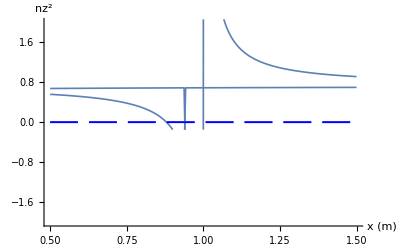

dataSet=Parallel Stratification 28HHz

xProfileMin=0.5

xProfileMax=1.5

nXmin=1.×10^18

nXmax=1.×10^18

BXmin=0.5

BXmax=1.5

freq=28000.

nz=0.5

etaList={0.,1.,0.,0.,0.}

xmin=0.5

xmax=1.5

```mathematica
nParallel2FS[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
 nzSqColdDisFS[freq,ne,b,nz,etaList]];
nt2FS=Table[Flatten[{x,nParallel2FS[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nF=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦2⟧}];
nS=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦3⟧}];
g1=PPComplexListPlot[nF,"x (m)","nz^2"];
g2=PPComplexListPlot[nS,"x (m)","nz^2"];
Show[{g1,g2},PlotRange->{-2.,2.}]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmax}];
```

### Plot Real and Imaginary parts of n_z from 4nd order cold plasma dispersion relation (Fast and Slow roots)

α = 0.1,  nx = 0.5

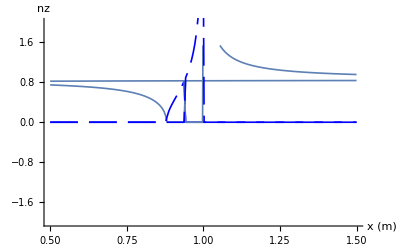

dataSet=Parallel Stratification 28HHz

xProfileMin=0.5

xProfileMax=1.5

nXmin=1.×10^18

nXmax=1.×10^18

BXmin=0.5

BXmax=1.5

freq=28000.

nz=0.5

etaList={0.,1.,0.,0.,0.}

xmin=0.5

xmax=1.5

```mathematica
nParallelFS[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
 nzColdDisFS[freq,ne,b,nz,etaList]];
nt2FS=Table[Flatten[{x,nParallelFS[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nF=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦2⟧}];
nS=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦3⟧}];
g1=PPComplexListPlot[nF,"x (m)","nz"];
g2=PPComplexListPlot[nS,"x (m)","nz"];
Show[{g1,g2},PlotRange->{-2.,2.}]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmax}];
```

### Plot Real and Imaginary parts of n_z^2 from 4nd order cold plasma dispersion relation (Plus and Minus roots)

α = 0.1,  nx = 0.5

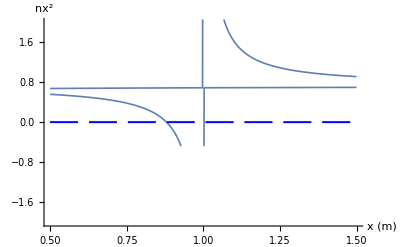

dataSet=Parallel Stratification 28HHz

xProfileMin=0.5

xProfileMax=1.5

nXmin=1.×10^18

nXmax=1.×10^18

BXmin=0.5

BXmax=1.5

freq=28000.

nz=0.5

etaList={0.,1.,0.,0.,0.}

xmin=0.5

xmin=0.5

```mathematica
nPerp2PM[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
		nzSqColdDisPM[freq,ne,b,nz,etaList]]
nt2PM=Table[Flatten[{x,nPerp2PM[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nP=Transpose[{Transpose[nt2PM]⟦1⟧,Transpose[nt2PM]⟦2⟧}];
nM=Transpose[{Transpose[nt2PM]⟦1⟧,Transpose[nt2PM]⟦3⟧}];
g1=PPComplexListPlot[nP,"x (m)","nx^2"];
g2=PPComplexListPlot[nM,"x (m)","nx^2"];
Show[{g1,g2},PlotRange->{-2.,2.}]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmin}];
```

## Plot Profiles

```mathematica
Plot[nprof[x],{x,xmin,xmax}]
```

-Graphics-

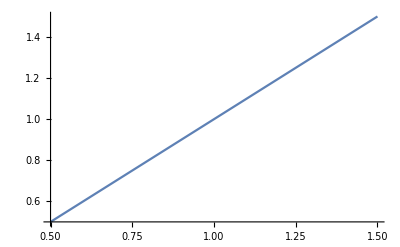

```mathematica
Plot[bprof[x],{x,xmin,xmax}]
```

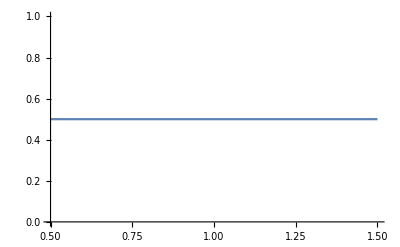

```mathematica
Plot[tprof[x],{x,xmin,xmax}]
```

```mathematica
αHcut[BXmax,freq, nz,1]
```

1.00015

## Initialization

#### Magnetic field,Density and Temperature Profiles

```mathematica
bprof[x_]:=If[Abs[(BXmax-BXmin)/BXmax]>10^-6,BXmin+(x-xProfileMin)/(xProfileMax-xProfileMin)(BXmax-BXmin),BXmin];
```

```mathematica
nprof[x_]:=If[Abs[(nXmax-nXmin)/nXmax]>10^-6,nXmin+(x-xProfileMin)/(xProfileMax-xProfileMin)(nXmax-nXmin),nXmin];
```

```mathematica
tprof[x_]:=If[Abs[(TXmax-TXmin)/TXmax]>10^-6,TXmin+(x-xProfileMin)/(xProfileMax-xProfileMin)(TXmax-TXmin),TXmin];
```

```mathematica
αHcut[B_,freq_, nz_,sgn_]:=(1-nz^2)×(1+sgn*2.79926 B/freq)
```